# Tables, Lists, and Importing Data

Upon successful completion of this lab, you should be able to:
1. Use the Table Command to make lists.
2. Extract information from lists.
3. Import data from spreadsheets into lists.
4. Sum the elements in a list.
5. Use lists to explore trends in data, to produce data for plotting, and as datasets on which to apply Simpson’s Rule for numerical integration.  

Instructions:
1. Read through the notebook top to bottom, executing cells as you go.
2. Complete the associated quiz in Canvas.

## The Table Command

The table command allows us to evaluate some argument or function over a set of values.  Suppose I had the function shown below and I wanted to evaluate it at several different inputs:  x=0,1,2,...10,.  I could first define the function and then use the “Table” command to “feed” those inputs to the function one at a time:

```mathematica
f[x_]=2x;
Table[f[i],{i,0,10}]
```

{0,2,4,6,8,10,12,14,16,18,20}

Note that the “i” in the command is a dummy variable and can be anything.  Below I’ve changed it to “x”:

```mathematica
Table[f[x],{x,0,10}]
```

{0,2,4,6,8,10,12,14,16,18,20}

Also note that I can easily change my starting and ending values for x, as well as my step size.  For instance, if I want to start at 2 and take steps of size .25 until I get to 5, the command would be:

```mathematica
Table[f[i],{i,2,5,.25}]
```

{4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

The braces, { }, around my output indicate that the output is a list.

## Using Lists

Now that we can create lists, we want to use them. First, to save us from typing the table command over and over, we can assign our list a name, for instance “list1”:

```mathematica
list1=Table[f[i],{i,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

Now I can recall this entire list by simply typing in the name:

```mathematica
list1
```

{2,4,6,8,10,12,14,16,18,20}

I can extract specific entries from a list by using double brackets as shown below, where I’m indicating I want the second entry in “list1”:

```mathematica
list1[[2]]
```

4

If I wanted to extract the second, third, fifth, and eighth entries of “list1” and put them into a new list called “list2”, I would use the following:

```mathematica
list2=list1[[{2,3,5,8}]]
```

{4,6,10,16}

If I wanted to extract the second through the fifth entries (inclusive) from “list1”, I would use double semicolons to indicate that:

```mathematica
list1[[2;;5]]
```

{4,6,8,10}

## Import Spreadsheet Data Into a List

Next we’ll explore importing data from a spreadsheet into Mathematica for analysis.  Do the following to get started:
1.  Download the spreadsheet “table_for_approx_int.xlsx” linked in Canvas to your desktop (or some other location that is convenient to access).  This spreadsheet simply contains two columns of data with headings t and d.
2.  Place your cursor inside the square brackets following the Import command below.
3.  From the top Mathematica menu bar, choose “Insert >> File Path...” 
4.  Locate and select the copy of “table_for_approx_int.xlsx” that you downloaded.  You should see the file name and associated path appear in gray.
5.  Evaluate the cell.

```mathematica
spreadsheet=Import["/home/cajacobs/Wolfram Mathematica/MTU/Quiz 5/table_for_approx_int.xlsx"]
```

{{{t,d},{0.,3.2},{3600.,2.7},{7200.,1.9},{10800.,1.7},{14400.,1.3},{18000.,1.},{21600.,1.1},{25200.,1.3},{28800.,2.8},{32400.,5.7},{36000.,7.1},{39600.,7.7},{43200.,7.9}}}

Notice above that each (t,d) pair appears inside braces, and two pairs of braces surround the output.  Mathematica uses braces around the entries of a matrix, so what we have at this point is a 14x2 matrix inside a 1x1 matrix.  It will be easier to work with our data if we extract the 14x2 matrix and call it “data”:

```mathematica
data=spreadsheet[[1]]
```

{{t,d},{0.,3.2},{3600.,2.7},{7200.,1.9},{10800.,1.7},{14400.,1.3},{18000.,1.},{21600.,1.1},{25200.,1.3},{28800.,2.8},{32400.,5.7},{36000.,7.1},{39600.,7.7},{43200.,7.9}}

Now we’ll extract each column of data and name the resulting lists t and d.  The syntax we’re using tells Mathematica to extract all rows of column 1 from “data” and put the result into list “t”:

```mathematica
t=data[[All,1]]
d=data[[All,2]]
```

{t,0.,3600.,7200.,10800.,14400.,18000.,21600.,25200.,28800.,32400.,36000.,39600.,43200.}

{d,3.2,2.7,1.9,1.7,1.3,1.,1.1,1.3,2.8,5.7,7.1,7.7,7.9}

We’ll revisit these two lists later on in an application involving Simpson’s Rule for numerical integration.

## Sum

### The Sum command

The sum command has the same structure as the Table command. The only difference is that instead of creating a list of values, it adds them all up. For example:

```mathematica
f[x_]=2x;
Table[f[i],{i,0,4}]
Sum[f[i],{i,0,4}]
```

{0,2,4,6,8}

20

Also, as with the Table command we can also changed the step size. For example:

```mathematica
Table[i,{i,0,2,.5}]
Sum[i,{i,0,2,.5}]
```

{0.,0.5,1.,1.5,2.}

5.

#### Pro Tip

You can also use the mathematical summation notation found in the palettes or by typing esc sumt esc

```mathematica
∑_(i=0)^10 i
```

55

## Applications

### Exploring Trends

Tables provide a convenient way to investigate what happens to function values as the input gets very big or very small. For instance, I should know that f(x)=x^2/2^x→0 as x→ ∞ , but if I was unsure, one way I could check is to look at the value of x^2/2^x as x goes from 1 to 100 counting by 10 as shown in the following table:

```mathematica
Table[x^2/2^x,{x,1,100,10}]//N
```

{0.5,0.059082,0.000210285,4.475×10^-7,7.6443×10^-10,1.15508×10^-12,1.61373×10^-15,2.13495×10^-18,2.71357×10^-21,3.34467×10^-24}

### Plotting Data

It is often more useful to look at a plot of data rather than looking at a list of the actual values. We can plot a list of values using the ListPlot command as shown below.

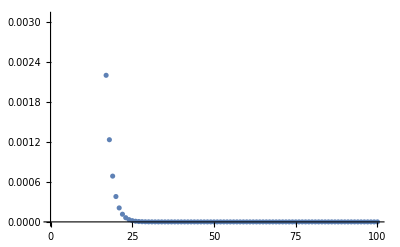

```mathematica
willplot=Table[x^2/2^x,{x,1,100}];
ListPlot[willplot]
```

The data suggest that x^2/2^x→0 as x→ ∞.  Note that this just helps me build a reasonable guess.  It is not a proof.

### Numerical Algorithms

In many algorithms we have to compute functions over a list of values. One example of this is Simpson’s Rule to numerically approximate definite integrals:
			∫_a^b f(x)ⅆx≈S_n=Δx/3[f(x_0)+4f(x_1)+2f(x_2)+4f(x_3)+...+2f(x_(n-2))+4f(x_(n-1))+f(x_n)]   where n is even and Δx=(b-a)/n.
The code below uses the Table and Sum commands in conjunction with this algorithm to approximate ∫_1^2 1/x ⅆx with n = 10.

```mathematica
a=1;
b=2;
n=10;
Δx=(b-a)/n;
f[x_]=1/x;
fvalues=Table[f[i],{i,a,b,Δx}]
SimpsonApprox1=Δx/3(fvalues[[1]]+4Sum[fvalues[[2i]],{i,1,n/2}]+2Sum[fvalues[[2i+1]],{i,1,n/2-1}]+fvalues[[n+1]])//N;
```

{1,10/11,5/6,10/13,5/7,2/3,5/8,10/17,5/9,10/19,1/2}

We generally use numerical integration techniques when a simple antiderivative for our function does not exist, making the Fundamental Theorem of Calculus challenging to apply, or when we do not have a formula to represent our function.  Let’s revisit the spreadsheet data you imported up above.  Recall that we named the lists representing the columns t and d :

```mathematica
t
d
```

{t,0.,3600.,7200.,10800.,14400.,18000.,21600.,25200.,28800.,32400.,36000.,39600.,43200.}

{d,3.2,2.7,1.9,1.7,1.3,1.,1.1,1.3,2.8,5.7,7.1,7.7,7.9}

In order to apply Simpson’s rule to this data we’ll need to modify our code slightly.  Δx will be replaced by Δt, which, since our t values are equally spaced, we can determine by subtracting any successive pair of values:

```mathematica
Δt=t[[3]]-t[[2]]
```

3600.

We’ll also need to calculate n, which represents the number of subintervals.  This value will be one less than the number of data points we have, but we’ll need to subtract 2 from the length of list d to account for the column heading appearing in the list:

```mathematica
n=Length[d]-2
```

12

Finally, we update our indexing so that the code grabs the desired entries from our list d:

```mathematica
SimpsonApprox2=Δt/3(d[[2]]+4	[d[[2i+1]],{i,1,n/2}]+2Sum[d[[2i]],{i,2,n/2}]+d[[n+2]])//N
```

143880.

## Remember, the best way to learn is to play with the examples and practice.

```mathematica
butts = Table[cats,{cats,0,5}]
```

{0,1,2,3,4,5}

```mathematica
butts[[1;;3]]
```

{0,1,2}

```mathematica
Table[(3+5 n^2)/(n+n^2),{n,900,1000}]//N
```

{4.99445,4.99446,4.99447,4.99447,4.99448,4.99448,4.99449,4.9945,4.9945,4.99451,4.99452,4.99452,4.99453,4.99453,4.99454,4.99455,4.99455,4.99456,4.99456,4.99457,4.99457,4.99458,4.99459,4.99459,4.9946,4.9946,4.99461,4.99462,4.99462,4.99463,4.99463,4.99464,4.99464,4.99465,4.99466,4.99466,4.99467,4.99467,4.99468,4.99468,4.99469,4.9947,4.9947,4.99471,4.99471,4.99472,4.99472,4.99473,4.99473,4.99474,4.99475,4.99475,4.99476,4.99476,4.99477,4.99477,4.99478,4.99478,4.99479,4.99479,4.9948,4.99481,4.99481,4.99482,4.99482,4.99483,4.99483,4.99484,4.99484,4.99485,4.99485,4.99486,4.99486,4.99487,4.99487,4.99488,4.99489,4.99489,4.9949,4.9949,4.99491,4.99491,4.99492,4.99492,4.99493,4.99493,4.99494,4.99494,4.99495,4.99495,4.99496,4.99496,4.99497,4.99497,4.99498,4.99498,4.99499,4.99499,4.995,4.995,4.99501}